## SSAPlot-example.m

LGPL Applies

```mathematica
<<xSSA.m
```

xSSAlite 1.2.01 (1-March-2011) loaded Tue-8-Mar-2011-11:32:55 using Mathematica 8.0 for Linux x86 (64-bit) (November 7, 2010)(8.0.0)

```mathematica
r={{A-> B, k1}, {B-> P, k2}, {P-> Q, k3}, {Q-> A, k4}}; 
myInitialConditions={A-> 100, B-> 0, P-> 0, Q-> 0};
myParameters={k1-> 1, k2-> 1, k3-> 1, k4-> 1};
rsim=SSA[r, 10, myInitialConditions, myParameters];
```

xSSA Exit. 930 steps.  929 points sampled.  0.097934 seconds.

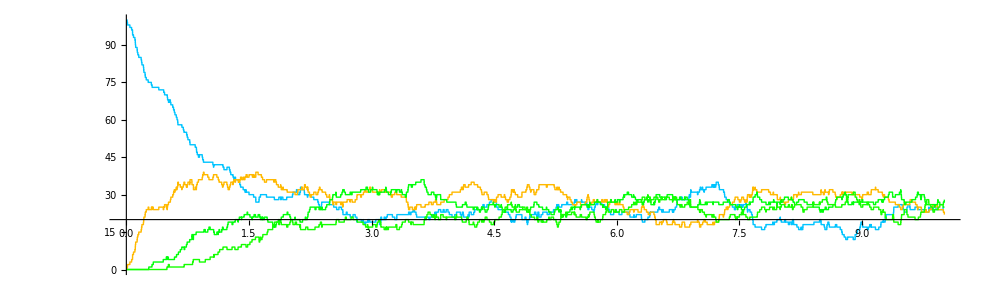

```mathematica
SSAPlot[rsim, {A, B, P, Q}, PlotRange-> {{0, 10}, All}, Background-> White, ImageSize-> 1000, AspectRatio-> .3]
```